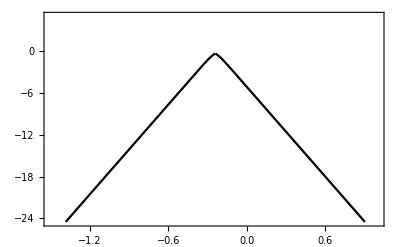

```mathematica
GH=EH+0.24;
k=8.617343*10^-5;
T=298;
h=4.13566743*10^-15;
v=k*T/h;
Hrate1=1*(1/(1+Exp[-GH/(k*T)]))*Exp[-GH/(k*T)];
Hrate2=1*(1/(1+Exp[-GH/(k*T)]));
Hratemax=Min[Hrate1,Hrate2];
volcano=Plot[0.55*Log[Hratemax],{EH,-1.5,1},Frame->True,FrameStyle->Directive[Thick,Black,18],Axes->{False,False,False},PlotRange->{-24.5,4.93},PlotStyle->Black]
```